```mathematica
gamma =1;
y = 1 - Exp[-x/gamma];
Series[y,{x,0,15}]
```

x-x^2/2+x^3/6-x^4/24+x^5/120-x^6/720+x^7/5040-x^8/40320+x^9/362880-x^10/3628800+x^11/39916800-x^12/479001600+x^13/6227020800-x^14/87178291200+x^15/1307674368000+O[x]^16

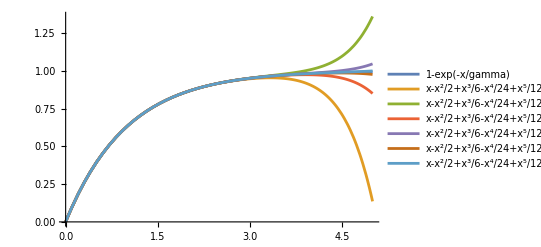

```mathematica
Plot[{1 - Exp[-x/gamma],Evaluate[Table[Normal[Series[y,{x,0,n}]],{n,10,15}]]},{x,0,5},PlotLegends->"Expressions"]
```